# How to use the radial solutions?

Mathematica Notebook created by Andreas Möri on Thursday 19th November 2020
EPFL ENAC IIC GEL
GC B1 385 (Bâtiment GC)
Station 18, 1015 Lausanne, Switzerland
Phone: +41 (0)21 693 44 70
andreas.mori@epfl.ch
Geo-energy Laboratory EPFL

contributors:
Brice Lecampion  - brice.lecampion@epfl.ch
Carlo Peruzzo - carlo.peruzo@epfl.ch

version n.: 0.0.1

!!IMPORTANT!!!
Before running the script and exploring all functionalities please enter the directory guiding towards your folder with the paclets below in the section “We load the relevant packages” as paclet directory.

#### Formatting the way of plotting

```mathematica
(*http://szhorvat.net/pelican/latex-typesetting-in-mathematica.html*)
(*ResourceFunction["MaTeXInstall"][];*) (* <-Run  once forevere *) 
Needs["MaTeX`"]
Myfontsize=22;
texStyle={FontFamily->"CMU Serif",FontSize->Myfontsize};
SetOptions[Plot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[LogLogPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLogPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLogLinearPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLogLogPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListVectorPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLinePlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
```

AbsoluteFileName::badfile: The specified argument  should be a valid string or File.

#### We load the relevant packages

Setting up the path to the directory of the GitFolder. You’ll need to adapt this in your case!

```mathematica
pacletDirectory = StringSplit[NotebookDirectory[],"\examples"][[1]]
PacletDirectoryLoad[pacletDirectory]
```

C:\Users\andeb\Documents\Wolfram Mathematica\PyFrac_Mathematica_postprocessing

{C:\Users\andeb\Documents\Wolfram Mathematica\PyFrac_Mathematica_postprocessing\,C:\Users\andeb\Documents\Wolfram Mathematica\PyFrac_Mathematica_postprocessing}

We simply load all the relevant packages. Based on this exercise

```mathematica
<<DescriptionUtilities`
<<NewtonianPulse`
<<RadialScaling`
<<ComputedSolutions`
<<PostProcessRadialPL`
<<RadialPowerLaw`
<<VertexSolutions`
<<rectangularMesh`
```

Get::noopen: Cannot open DescriptionUtilities`.

$Failed

Get::noopen: Cannot open NewtonianPulse`.

$Failed

Get::noopen: Cannot open RadialScaling`.

$Failed

Get::noopen: Cannot open ComputedSolutions`.

$Failed

Get::noopen: Cannot open PostProcessRadialPL`.

$Failed

Get::noopen: Cannot open RadialPowerLaw`.

$Failed

Get::noopen: Cannot open VertexSolutions`.

$Failed

Get::noopen: Cannot open rectangularMesh`.

$Failed

#### Defining the set of parameters of your experiment

We define the parameters of our simulations.

For most of them we have two options.

Take for example the plain strain modulus  E'=E/(1-ν^2), you can either define in by directly passing E', or by seperately passing the Young’s modulus E as Emod (this is necessary as  E is protected by Mathematica as the Euler constant), and the Poisson’s ratio ν.

Similarly, you can provide directly the adapted fluid viscosity μ'=12 μ or simply the viscosity μ. The same principle goes for the other adapted parameters.

Note that if no fluid index n is provided the default value of n=1 is considered.

A note on the total injected volume Vo, this quantity can be entered either by giving simultaneously Qo and ts, or by directly passing Vo.

A final note is put on the fact that fore some scalings we would like to use directly KIc instead of K'. This is possible with an options which one can set to true. We will come back to this during the examples.

A particulairty for buoyancy solutions is that additionally one gets a buoyancy Δγ. Other possible incorporations are a stress contrast or neutral buoyancy level.

Here you load the data of the simulation

```mathematica
dirFiles =NotebookDirectory[];
simulation = "Mb1e-3_SJ_2o0"
```

Mb1e-3_SJ_2o0

```mathematica
LoadBuoyancyData[simulation]
```

Now all the data is loaded (We show as an example the properties)

```mathematica
Mb1em3SJ2o0prop
```

{KIc→1.3822×10^6,Ep→1.06667×10^9,Cp→0.,Qo→0.05,μp→0.012,Δγ→490.5,sl→{0.,-2.84217×10^-14},dl→400,SJ→2.}

We show here the outcome of the two parameter sets for the user to understand.

As to do so we load a part of the paclet normally hidden to the end user (as the details are not important

```mathematica
<<UtilityForScalings`
(* You see that the results adapt in function of your choice of input parameter.
Note that Mp = μ' *)
inputDataTransformation[Mb1em3SJ2o0prop]
```

Get::noopen: Cannot open UtilityForScalings`.

$Failed

inputDataTransformation[{KIc→1.3822×10^6,Ep→1.06667×10^9,Cp→0.,Qo→0.05,μp→0.012,Δγ→490.5,sl→{0.,-2.84217×10^-14},dl→400,SJ→2.}]

```mathematica
(* And finally we give the option to use directly KIc as Kp by setting its boolean to true *)
inputDataTransformation[Mb1em3SJ2o0prop,False]
```

{Ep→1.06667×10^9,Vo→0.05 ts,Qo→0.05,ts→ts,Mp→0.012,Kp→1.3822×10^6,Cp→0.,n→1.}

#### Generalities

It is possible to get informations about every symbol and function that can by used by sympling entering a question mark ? in front of the function.

```mathematica
?toNumericalScaling
```

The parameter set defined previously will be generally used for this functions as an argument to pass. 

Further we would like to emphasize that generally four Vertexes are present and can be accessed as:
	- viscosity storage regime “M”
	- toughness storage regime “K”
	- viscosity leak-off regime “Mt”
	- toughness leak-off regime “Kt”
	
Scalings generally return the characteristic lengthscal Lstar, opening scale wstar, net pressure scale pstar, the flux scale qstar (only for viscosity related scalings) as well as the corresponding dimensionless numbers 𝒦 (dimensionless toughness), ℳ (dimensionless viscosity), 𝒞 (dimensionless leak-off coefficient) and 𝒱 (dimensionless storage coefficient)
	
We also have some near vertex solutions which can notably be accessed as:
	- toughness storage solution with first order viscosity “KVisc”
	- toughness storage solution with first order leak-off “KLeak”
	- toughness leak-off solution with first order storage “KtStor”
	
Generally it is always possible to get a scaling in it’s dimensionless form or in a dimensional form. As to do so a flag is implemented allowing you to decide which form do you need.

#### Recover a scaling in function of the parameters

It is often useful to recover a specific scaling in function of the parameters. This can simply be done by passing it the wished vertex (see generalities for the definitions), an empty parameter set and the (non defined!) variable t as time.

```mathematica
(* Displaying the characteristcal scales and the dimensionless parameters of the M-Vertex scaling *)
vertexScaling["M",{},t]
```

{Lstar→(Ep^0.111111 Qo^(1/3) t^0.444444)/μp^0.111111,wstar→(Qo^(1/3) t^0.111111 μp^0.222222)/Ep^0.222222,pstar→(Ep^0.666667 μp^0.333333)/t^0.333333,qstar→(Qo^(2/3) μp^0.111111)/(Ep^0.111111 t^0.444444),𝒦→(Kp t^(1/9))/(Ep^(13/18) Qo^(1/6) μp^(5/18)),𝒞→(Cp Ep^(2/9) t^(7/18))/(Qo^(1/3) μp^(2/9))}

```mathematica
(* Displaying the characteristcal scales and the dimensionless parameters of the Kt-Vertex scaling *)
vertexScaling["Kt",{},t]
```

{Lstar→(√Qo t^(1/4))/(√Cp),wstar→(Kp Qo^(1/4) t^(1/8))/(Cp^(1/4) Ep),pstar→(Cp^(1/4) Kp)/(Qo^(1/4) t^(1/8)),qstar→(√Cp √Qo)/t^(1/4),ℳ→(√Cp Ep^3 √Qo μp)/(Kp^4 t^(1/4)),𝒱→(Cp^(5/4) Ep t^(3/8))/(Kp Qo^(1/4))}

```mathematica
(* The same is possible for the pulse (block injection) scalings *)
pulseVertexScalings["K",{},t]
pulseVertexScalings["Mt",{},t]
```

{Lstar→(Ep^(2/5) (Qo ts)^(2/5))/Kp^(2/5),wstar→(Kp^(4/5) (Qo ts)^(1/5))/Ep^(4/5),pstar→Kp^(6/5)/(Ep^(1/5) (Qo ts)^(1/5)),ℳ→(Ep^(13/5) (Qo ts)^(3/5) μp)/(Kp^(18/5) t),𝒞→(Cp Ep^(4/5) √t)/(Kp^(4/5) (Qo ts)^(1/5))}

{Lstar→(√(Qo ts))/(√Cp t^(1/4)),wstar→((Qo ts)^(3/8) μp^(1/4))/(Cp^(1/8) Ep^(1/4) t^(5/16)),pstar→(Cp^(3/8) Ep^(3/4) μp^(1/4))/(t^(1/16) (Qo ts)^(1/8)),𝒦→(Kp t^(3/16))/(Cp^(1/8) Ep^(3/4) (Qo ts)^(1/8) μp^(1/4)),𝒱→(Cp^(9/8) Ep^(1/4) t^(13/16))/((Qo ts)^(3/8) μp^(1/4))}

#### Recover a vertex solution

We will now show you how to load the vertex solutions. First let’s consider an injection solution which is loaded by the following function.

```mathematica
?injectionVertexSolutions
```

The above gives you the way how to load it. We will perform this with our two parameter sets with two configuratios below.

```mathematica
injectionVertexSolutions["M",Mb1em3SJ2o0prop,0.2,{1,70,635,10^3}]
```

{FractureLength→{4.23125,27.9584,74.4982,91.1595},Opening→{0.00151577,0.00243021,0.00310494,0.00326563},NetPressure→{179127.,43463.9,20840.3,17912.7}}

```mathematica
injectionVertexSolutions["K",Mb1em3SJ2o0prop,0.7,10^2,False,False]
```

{FractureLength→(3/π)^(2/5)/2^(1/5),Opening→0.466833,NetPressure→π^(6/5)/(8 2^(2/5) 3^(1/5)),FluidFlux→0.208606}

The first parameter passed is the regime (see generalities for the options), the second is the set of parameters, the third is the dimensionless position within the fracture ρ (we will describe this below), the fourth the time at which we consider the solution (either a list or a single value). 

The fifth and sixth entrie are obtional booleans. If the fifth is set to false you will get the dimensionless solution (as default you get the dimensional solution). If the sixth is set to False we will use KIc directly instead of transforming it to K’.

The output given is the FractureLength (the radius of the fracture or the prefactor if dimensionless), Opening (at the ρ given) and the NetPressure (also given at ρ).

Plotting a profile

We will now give a definition of ρ and detail what we mean by dimensionless solutions. As such we are plotting the profile of the opening of a viscosity leak-off dominated fracture in function of the normalized x coordinate (along R) which is the definition of ρ = x/R.

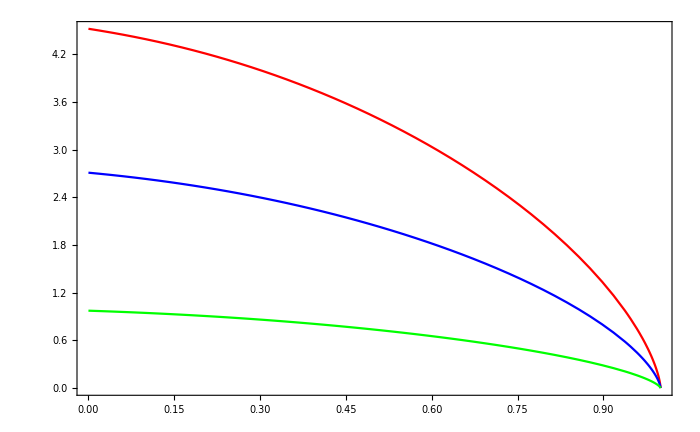
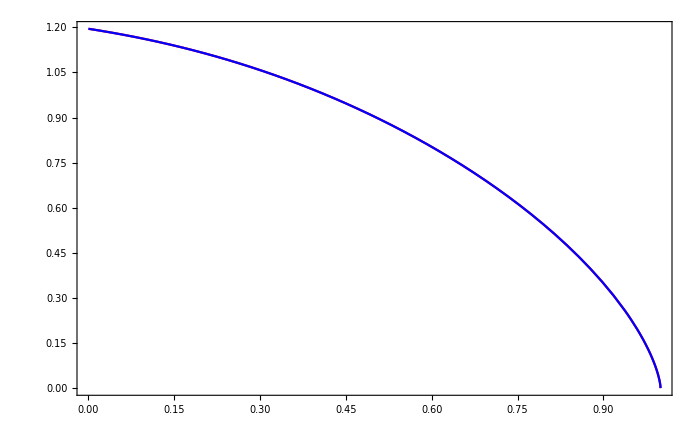

```mathematica
{Show[Plot[Opening  10^3/.injectionVertexSolutions["M",Mb1em3SJ2o0prop,ρ,10^4],{ρ,0,1},PlotStyle->Red,PlotLegends->{MaTeX[" t=10\\textsuperscript{4} ",FontSize->Myfontsize-2]}],
Plot[Opening 10^3/.injectionVertexSolutions["M",Mb1em3SJ2o0prop,ρ,10^2],{ρ,0,1},PlotStyle->Blue,PlotLegends->{MaTeX[" t=10\\textsuperscript{2} ",FontSize->Myfontsize-2]}],
Plot[Opening 10^3/.injectionVertexSolutions["M",Mb1em3SJ2o0prop,ρ,10^-2],{ρ,0,1},PlotStyle->Green,PlotLegends->{MaTeX[" t=10\\textsuperscript{-2} ",FontSize->Myfontsize-2]}],
PlotRange-> All,FrameLabel->{MaTeX["x/R = \\rho \\text{ [-]}",FontSize->Myfontsize],MaTeX["w \\text{ [mm]}",FontSize->Myfontsize]}],
Show[Plot[Opening/.injectionVertexSolutions["M",Mb1em3SJ2o0prop,ρ,10^4,False],{ρ,0,1},PlotStyle->Red,PlotLegends->{MaTeX[" t=10\\textsuperscript{4} ",FontSize->Myfontsize-2]}],
Plot[Opening/.injectionVertexSolutions["M",Mb1em3SJ2o0prop,ρ,10^2,False],{ρ,0,1},PlotStyle->Blue,PlotLegends->{MaTeX[" t=10\\textsuperscript{2} ",FontSize->Myfontsize-2]}],
Plot[Opening/.injectionVertexSolutions["M",Mb1em3SJ2o0prop,ρ,10^-2 False],{ρ,0,1},PlotStyle->Green,PlotLegends->{MaTeX[" t=10\\textsuperscript{-2} ",FontSize->Myfontsize-2]}],
PlotRange-> All,FrameLabel->{MaTeX["x/R = \\rho \\text{ [-]}",FontSize->Myfontsize],MaTeX["w/W = \\Omega \\text{ [-]}",FontSize->Myfontsize]}]}
```

The first plot shows the dimensional opening in function of the normalized fracture length (we recomend to use the normalized fracture length for better comparison [see next figure vor an example]). Using the scaling one can observe that the curves collapse to one single curve independent of the time.

Transpose::nmtx: The first two levels of {{0.,0.001 FractureLength,0.002 FractureLength,0.003 FractureLength,0.004 FractureLength,0.005 FractureLength,0.006 FractureLength,0.007 FractureLength,0.008 FractureLength,«33»,0.042 FractureLength,0.043 FractureLength,0.044 FractureLength,0.045 FractureLength,0.046 FractureLength,0.047 FractureLength,0.048 FractureLength,0.049 FractureLength,«951»},«7»} cannot be transposed.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^0.333333 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Transpose::nmtx: The first two levels of {{0.,0.001 FractureLength,0.002 FractureLength,0.003 FractureLength,0.004 FractureLength,0.005 FractureLength,0.006 FractureLength,0.007 FractureLength,0.008 FractureLength,«33»,0.042 FractureLength,0.043 FractureLength,0.044 FractureLength,0.045 FractureLength,0.046 FractureLength,0.047 FractureLength,0.048 FractureLength,0.049 FractureLength,«951»},«7»} cannot be transposed.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Transpose::nmtx: The first two levels of {{0.,0.001 FractureLength,0.002 FractureLength,0.003 FractureLength,0.004 FractureLength,0.005 FractureLength,0.006 FractureLength,0.007 FractureLength,0.008 FractureLength,«33»,0.042 FractureLength,0.043 FractureLength,0.044 FractureLength,0.045 FractureLength,0.046 FractureLength,0.047 FractureLength,0.048 FractureLength,0.049 FractureLength,«951»},«7»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

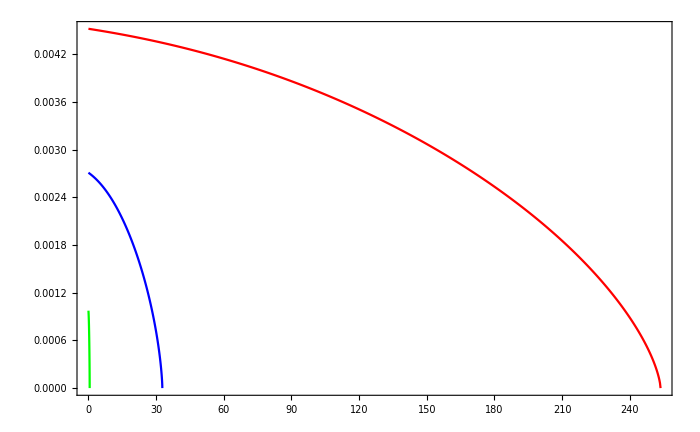

```mathematica
Show[ListPlot[{FractureLength #,Opening}ᵀ/.injectionVertexSolutions["M",Mb1em3SJ2o0prop,#,10^4]&@Range[0,1,0.001],Joined-> True,PlotStyle->Red,PlotLegends->{MaTeX[" t=10\\textsuperscript{4} ",FontSize->Myfontsize-2]}],ListPlot[{FractureLength #,Opening}ᵀ/.injectionVertexSolutions["M",Mb1em3SJ2o0prop,#,10^2]&@Range[0,1,0.001],Joined-> True,PlotStyle->Blue,PlotLegends->{MaTeX[" t=10\\textsuperscript{2} ",FontSize->Myfontsize-2]}],ListPlot[{FractureLength #,Opening}ᵀ/.injectionVertexSolutions["M",Mb1em3SJ2o0prop,#,10^-2]&@Range[0,1,0.001],Joined-> True,PlotStyle->Green,PlotLegends->{MaTeX[" t=10\\textsuperscript{-2} ",FontSize->Myfontsize-2]}],
PlotRange-> All,FrameLabel->{MaTeX["R \\text{ [m]}",FontSize->Myfontsize],MaTeX["w \\text{ [mm]}",FontSize->Myfontsize]}]
```

It is obvius that such A plot is hard to read and merely hids a lot of useful information.

Plotting a Fracture evolution

We can also plot the evolution of a fracture in time. We show an example of such a plot hereafter for the two parameter sets and a toughness dominated fracture evolution.

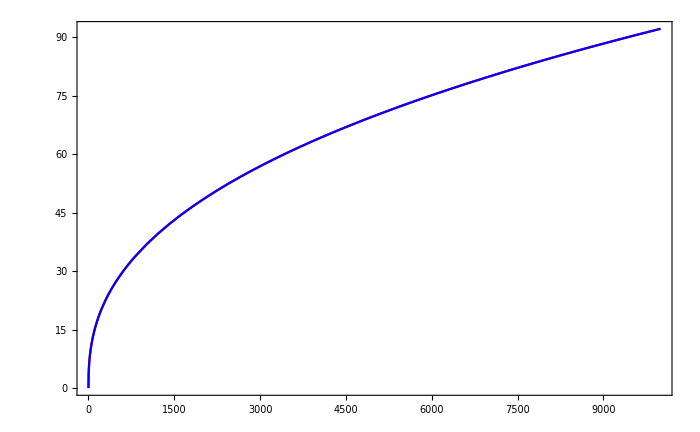

```mathematica
Show[Plot[FractureLength/.injectionVertexSolutions["K",Mb1em3SJ2o0prop,.5,t],{t,10^-4,10^4},PlotStyle->Red,PlotLegends->{MaTeX[" \\text{parameter set 1} ",FontSize->Myfontsize-2]}],
Plot[FractureLength/.injectionVertexSolutions["K",Mb1em3SJ2o0prop,.5,t],{t,10^-4,10^4},PlotStyle->Blue,PlotLegends->{MaTeX[" \\text{parameter set 2} ",FontSize->Myfontsize-2]}],
PlotRange-> All,FrameLabel->{MaTeX["t \\text{ [s]}",FontSize->Myfontsize],MaTeX["R \\text{ [m]}",FontSize->Myfontsize]}]
```

Note that the near vertex solutions can easily be plotted in the same way.

#### Plot some footprints

We will now show you how to plot a set of footprints  in a colored way

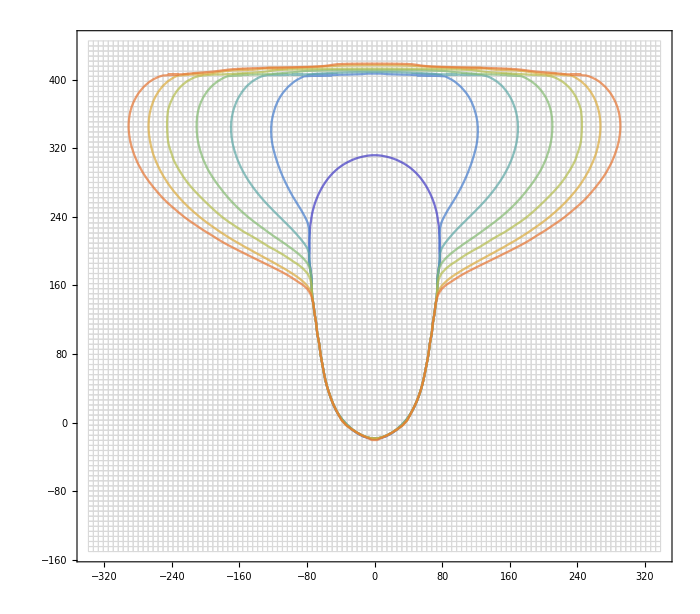

```mathematica
(* generating the fooprints correctly and getting the background *)
plotInfos = coloredFootprints[simulation, False];

(* Get the simulation name in the correct way *)
sim=StringReplace[simulation,"_"->""];
sim =StringReplace[sim,"-"->"m"];
sim =StringReplace[sim,"+"->"p"];

(* We generate the legend and the labels *)
Legendi=Round[Symbol[sim<>"fractures"]["time"],0.0001];
xlabel=MaTeX`MaTeX["x \\text{ [m]}",FontSize->Myfontsize];
ylabel=MaTeX`MaTeX["y \\text{ [m]}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,PlotRange->All,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend["Rainbow",MaTeX`MaTeX[#,FontSize->Myfontsize-2]&/@Legendi,LegendLabel->Column@MaTeX[{"\\text{Numerical data:}","\\text{(time [s])}"},FontSize->Myfontsize]]};

(* Plooting the colored footprints *)
Superposition=Show[("Background"/.plotInfos),ListPlot["Footprints"/.plotInfos,Joined->True,optlegend,PlotStyle->"Style"/.plotInfos],opt]
```

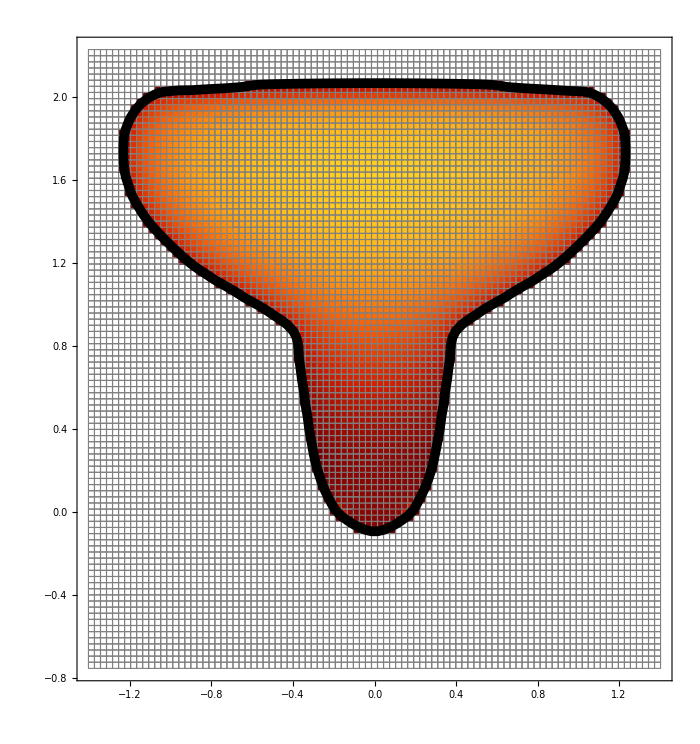

```mathematica
(* Get the simulation name in the correct way *)
sim=StringReplace[simulation,"_"->""];
sim =StringReplace[sim,"-"->"m"];
sim =StringReplace[sim,"+"->"p"];

(* generating the footrpint correctly and getting the background *)
index =6;
plotInfos =get2DDistributions[simulation,index];

(* We generate the legend and the labels *)
xlabel=MaTeX["x \\text{ [m]}",FontSize->Myfontsize];
ylabel=MaTeX["y \\text{ [m]}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,PlotRange->All,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->("Legend"/.plotInfos)};

(* Plooting the colored footprints *)
Superposition=Show[("Graphics"/.plotInfos),ListPlot[{(Symbol[sim <>"fractures"]["fp_x"][["Index"/.plotInfos]])/(KIc^(2/3)/Δγ^(2/3)/.Symbol[sim<>"prop"]),(Symbol[sim <>"fractures"]["fp_y"][["Index"/.plotInfos]])/(KIc^(2/3)/Δγ^(2/3)/.Symbol[sim<>"prop"])}ᵀ,Joined->True,PlotStyle->{Black,Thickness[.01]},optlegend],optlegend,opt]
```

## Some specific functions are defined hereafter

Load the buoyant data

```mathematica
LoadBuoyancyData[simName_]:=Module[{sim},
(* Put the string in a form that can be used as a symbol by mathematica *)
sim=StringReplace[simName,"_"->""];
sim =StringReplace[sim,"-"->"m"];
sim =StringReplace[sim,"+"->"p"];

(* Check if the symobl already exists else delete it *)
If[ValueQ[Evaluate[Symbol[sim]]],
Clear[Symbol[sim]];];

Evaluate[Symbol[sim]] =Association[Import[dirFiles<>simName<>"_geometrics.json"]]; (* Load geometrical data *)

(* Check if the symobl already exists else delete it *)
If[ValueQ[Evaluate[Symbol[sim<>"prop"]]],
Clear[Symbol[sim<>"prop"]];];

(* Load properties dictionary *)
If[KeyExistsQ[Symbol[sim],"Vo"],
Evaluate[Symbol[sim<>"prop"]] = {KIc-> √(π/32)Symbol[sim]["Kp"],Ep-> Symbol[sim]["Ep"],Cp-> Symbol[sim]["Cp"],Qo-> Symbol[sim]["Qo"],μp-> Symbol[sim]["mup"],Δγ-> Symbol[sim]["Dgamma"],Vo-> Symbol[sim]["Qo"] * Symbol[sim]["ts"],ts-> Symbol[sim]["ts"],sl-> Symbol[sim]["sources_coordinates"],dl->Symbol[sim]["dlayer"],SJ->  Symbol[sim]["SJ"]};,
Evaluate[Symbol[sim<>"prop"]] = {KIc-> √(π/32)Symbol[sim]["Kp"],Ep-> Symbol[sim]["Ep"],Cp-> Symbol[sim]["Cp"],Qo-> Symbol[sim]["Qo"],μp-> Symbol[sim]["mup"],Δγ-> Symbol[sim]["Dgamma"],sl-> Symbol[sim]["sources_coordinates"],dl->Symbol[sim]["dlayer"],SJ->  Symbol[sim]["SJ"]};];

(* Check if the symobl already exists else delete it *)
If[ValueQ[Evaluate[Symbol[sim<>"fractures"]]],
Clear[Symbol[sim<>"fractures"]];];

(* Load footprints and so on *)
Evaluate[Symbol[sim<>"fractures"]] = Association[Import[dirFiles<>simName<>"_fractures.json"]];

(* Check if the symobl already exists else delete it *)
If[ValueQ[Evaluate[Symbol[sim<>"sections"]]],
Clear[Symbol[sim<>"sections"]];];

(* Load sections *)
Evaluate[Symbol[sim<>"sections"]] = Association[Import[dirFiles<>simName<>"_sections.json"]];

];
```

With this function one can plot footprints in different colors

```mathematica
(* Function to get necessary ingredients for colored footprints *)
coloredFootprints[sim_, dimless_:True]:=Module[{LastMesh,stringSim, footprints, styling, bck, divider,iter},
(* Put the string in a form that can be used as a symbol by mathematica *)
stringSim=StringReplace[sim,"_"->""];
stringSim =StringReplace[stringSim,"-"->"m"];
stringSim =StringReplace[stringSim,"+"->"p"];


(* Decide if to plot in dimensionless form *)
If[dimless ,divider =KIc^(2/3)/Δγ^(2/3)/.Symbol[stringSim<>"prop"];,
divider = 1;];

(* Generate the mesh of the last footprint *)
LastMesh =rectangularMesh`meshPlan[0,0,0,0,Symbol[stringSim <>"fractures"]["mesh_info"][[-1]]];

(* We need to order the footprints correctly *)
footprints = ConstantArray[0,{Length[Symbol[stringSim <>"fractures"]["time"]],1}];
For[iter = 1,iter≤ Length[Symbol[stringSim <>"fractures"]["time"]],iter ++,
footprints[[iter]]={Symbol[stringSim <>"fractures"]["fp_x"][[iter]],Symbol[stringSim <>"fractures"]["fp_y"][[iter]]}ᵀ/divider;
];

(* Define the style of footprints *)
styling =Thread@{Thick,Opacity[0.7],ColorData["Rainbow"]/@Range[0,1,1/Length[Symbol[stringSim <>"fractures"]["time"]]]};

(* Generate the background mesh *)
bck =Graphics[{EdgeForm[{Thin,LightGray}],Transparent,GraphicsComplex[LastMesh["vertexes"]/divider,Polygon[LastMesh["conn"][[1;;]]]]}];

(* Output the style *)
{"Style"-> styling, "Footprints"-> footprints, "Background"-> bck, "LastMesh"-> LastMesh}

];
```

With this function one can Plot opening or pressure distribution within the crack

```mathematica
get2DDistributions[sim_,index_,dimless_:True,var_:"w"]:=Module[{stringSim,ind, theMesh, scale, Cdat, graphics, TheColor, iter, pn, Leg, limits,divider},

(* Put the string in a form that can be used as a symbol by mathematica *)
stringSim=StringReplace[sim,"_"->""];
stringSim =StringReplace[stringSim,"-"->"m"];
stringSim =StringReplace[stringSim,"+"->"p"];

(* Check if the index is ok *)
If[Abs[index]≥ Length[Symbol[stringSim <>"fractures"]["time"]],
ind =Sign[index] Length[Symbol[stringSim <>"fractures"]["time"]];
Print["Index was out of range so limiting index was taken instead"];,
ind = index;
];

(* Get the corresponding mesh *)
theMesh =rectangularMesh`meshPlan[0,0,0,0,Symbol[stringSim <>"fractures"]["mesh_info"][[ind]]];

If[dimless,
divider = KIc^(2/3)/Δγ^(2/3)/.Symbol[stringSim <>"prop"];
,
divider = 1;
];
(* Load opening or pressure in function of var *)
If[var == "w",
scale =Rescale[Symbol[stringSim <>"fractures"]["w"][[ind]],{Min[Symbol[stringSim <>"fractures"]["w"][[ind]]],Max[Symbol[stringSim <>"fractures"]["w"][[ind]]]}];
limits = {Min[Symbol[stringSim <>"fractures"]["w"][[ind]]],Max[Symbol[stringSim <>"fractures"]["w"][[ind]]]};
,
pn=Symbol[stringSim <>"fractures"]["pn"][[ind]];
pn[[Flatten[Position[Symbol[stringSim <>"fractures"]["pn"][[ind]],_?(#≥ 0.0&)]]]]=0;
scale =Rescale[pn,{Min[pn],Max[pn]}];
limits = {Min[pn],Max[pn]};
];

(* Generate the graphics *)
Cdat =ColorData["SolarColors"]/@scale[[1;;]]; 
graphics =ConstantArray[0,{Length[scale],1}];
For[iter = 1,iter≤ Length[scale],iter++,
If[scale[[iter]] == 0,TheColor=Transparent;,TheColor =Cdat[[iter]];];
graphics[[iter]]=Graphics[{EdgeForm[{Thin,Gray}],TheColor,Polygon[(theMesh["vertexes"][[theMesh["conn"][[iter]]]])/divider]}];
];

(* Generate the legend *)
If[dimless,
If[var ≠ "pn",
Leg =BarLegend[{"SolarColors",limits/(KIc^(4/3)/(Ep Δγ^(1/3))/.Symbol[stringSim <>"prop"])},LegendLayout->"Row",LegendLabel->MaTeX["w/W",FontSize->Myfontsize]];
,
Leg =BarLegend[{"SolarColors",limits/(KIc^(2/3) Δγ^(1/3)/.Symbol[stringSim <>"prop"])},LegendLayout->"Row",LegendLabel->MaTeX["pn/P",FontSize->Myfontsize]];
];
,
If[var ≠ "pn",
Leg =BarLegend[{"SolarColors",limits},LegendLayout->"Row",LegendLabel->MaTeX["w \\text{ [mm]}",FontSize->Myfontsize]];
,
Leg =BarLegend[{"SolarColors",limits 1000},LegendLayout->"Row",LegendLabel->MaTeX["pn \\text{ [MPa]}",FontSize->Myfontsize]];
];
];

(* Output data *)
{"Mesh"-> theMesh,"Scale"-> scale,"Graphics"-> graphics,"Index"-> ind, "Legend"-> Leg}
];
```